# homework说明文档

张晨晖 asterix314@163.com

## 文件列表

buffer.hpp - 共享队列及常量定义

subscriber.cpp - 订阅者逻辑

publisher.cpp - 发布者逻辑

test.sh - 测试脚本

makefile - 编译脚本

homework.pdf - 说明文档（本文件）

## 设计要点

题目要求进程间通信时延尽量小，因此考虑使用共享内存。publisher和subscriber通过共享内存传输数据，省去了数据拷贝过程，节约时间。

C++的实现中，主要使用了boost.interprocess提供的共享内存支持。在共享内存空间中存放了一些用于同步的信号量和一个队列。两个publisher从队列头部写入数据，一个subscriber从队列尾部取出数据。这些进程互斥地使用队列。subscriber负责创建共享内存。之后就不断试图从队列中取数，队列空则等待。每个publisher每隔1毫秒向队列写入数据，写完规定的数目（1000条）后即退出。subscriber在取出所有的数据（2000条）后，负责销毁共享内存并退出。

为了验证写入的数据最后都被读取出来，publisher向队列写入的数据区域（256字节）的最前面是一个递增的整数。publisher 1 写入0、1、2、……999，publisher 2写入1000、1001、1002、……1999。subscriber将取出的数字排序后就可以验证写入和读取过程都没有出现遗漏。随数据写入的还有当前时间。其与读取时当前时间的差（以微秒计）即为时延。

程序使用boost.accumulator库提供的统计函数对时延进行分析，计算平均值、标准差等统计量并输出。同时把所有原始时延记录保存为文本文件delays.txt供进一步分析。

## 工具版本及运行结果

编码使用的boost版本1.65.1，编译器为clang++版本4.0.1，在Cygwin + Windows 10系统上编译并运行正常。输出样例：

$ ./test.sh
homework test
[S1] starts.
[S1] size of shared buffer set to 4248 bytes.
[S1] created shared buffer 'homework' at 0x6ffffff0000
[S1] receiving messages ...
[P1] starts.
[P1] opened shared buffer 'homework' at 0x6ffffff0000
[P1] sending 1000 messages ...
[P2] starts.
[P2] opened shared buffer 'homework' at 0x6ffffff0000
[P2] sending 1000 messages ...
[P1] exit.
[P2] exit.
[S1] check received messages: ok.
[S1] statistics of delays in micro seconds:
[S1] min = 0 max = 16264.4 mean = 598.904 std = 2847.34
[S1] remove shared buffer and exit.

## 时延分析

程序输出的2000个时延数据导入Mathematica进行绘图。发现时延数据集中于两类：大于15ms的和小于1ms的。其中小于1ms的占多数，而此中绝大多数又居于50us以下。

```mathematica
delays=Import["C:\\cygwin64\\home\\zhangchenhui\\work\\vquant-homework\\delays.txt","List"];
```

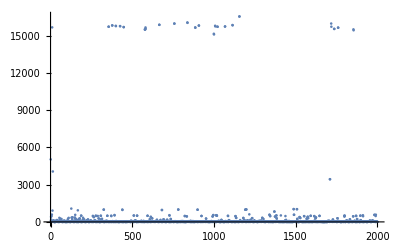

```mathematica
ListPlot[delays,PlotRange->All]
```

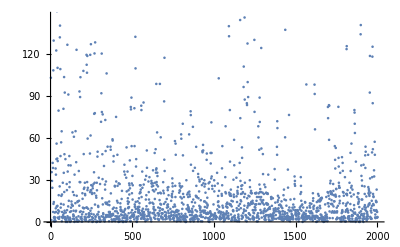

```mathematica
ListPlot[delays]
```

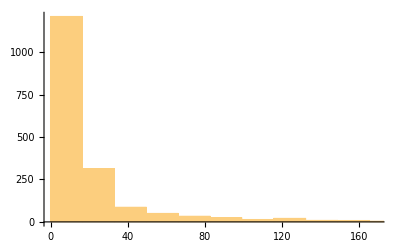

```mathematica
Histogram[delays]
```

可见系统没有收到扰动的情况下时延应该在50us以下，这主要是由publisher / subscriber进程切换和同步操作带来的。超过1ms的时延猜测是由来自本系统外的原因导致，比如CPU切换到其他耗时进程、换页、输入输出等。改进的方向应该是尽量将这些外部扰动隔离，比如增加publisher / subscriber的处理器优先级，关闭其他无关进程等等。